## Reflection Amplitude in a Kerr Background Based on: Richard Brito, Vitor Cardoso and Paolo Pani, “Black hole superradiance: from fundamental physics to astrophysics” (2015)

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Teukolsky’s equation

Here we write Teukolsky’s equation with in wave-like form

### Useful definitios

```mathematica
$Assumptions={M>0,a> 0,r>0,a<M,ω>0};
Δ[r_]:=r^2+a^2-2 M r;
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);
Ωh=a/(rplus^2+a^2);
f[r_]:=Δ[r]/(r^2+a^2);
```

#### Wave equation

```mathematica
V=(KK^2-2I s(r-M)KK+Δ[r](4I s ω r-λ))/((r^2+a^2)^2)-G[r]^2-f[r]G'[r];
G[r_]:=(s(r-M))/(r^2+a^2)+(r Δ[r])/((r^2+a^2)^2);
KK=(r^2+a^2)ω-a m;
eqn=f[r]^2 R''[r]+f'[r]f[r]R'[r] +V R[r]//Simplify;
```

### Equations and Series [You need to run this only the first time]

#### Series Horizon (takes a while)

Here we do the standard series expansion at the horizon for the equation and its solution. The series is in (r-rplus)^i. You can set the order of the expansion depending on the numerical stability you need.

```mathematica
R[r_]:=(r-rplus)^AA(r-rplus)^(-s/2)(r-rminus)^(-s/2) h[r];
eqn1=eqn/(r-rplus)^AA(r-rplus)^(s/2)(r-rminus)^(s/2)//Simplify;
Clear[R]
```

```mathematica
ORDH=8;
h[r_]:=Sum[hh[i] (r-rplus)^i,{i,0,ORDH}]; 
ruleH={AA->(ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2))};
ss=Series[eqn1//.ruleH,{r,rplus,ORDH}]//Chop//Simplify;
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,1,ORDH}];
yh=Table[hh[i],{i,1,ORDH}];
Length[eqsH]
Length[yh]
seriesH=Solve[eqsH,yh][[1]]//Simplify;
seriesH=Union[seriesH,ruleH];
Clear[h]
```

8

8

#### Series infinity (takes a while)

Here we do the standard series expansion at infinity for the equation and its solution. The series is in (r)^-i. Again, you can set the order of the expansion depending on the numerical stability you need.

```mathematica
R[r_]:=Exp[kk r] r^AA H[r];
eq1b=eqn/(ⅇ^(kk  r)r^AA)//Simplify;
Clear[R]
```

```mathematica
ORDINF=7;
H[r_]:=Sum[hhinf[i] r^-i,{i,0,ORDINF+10}];
ruleINF={kk^2->-ω^2,AA->(-ⅈ s ω-2 M ω^2)/kk,kk^4->ω^4,kk^6->-ω^6};
ss1=Series[{eq1b}//.ruleINF,{r,∞,ORDINF}]//Chop;

eqs1=Table[SeriesCoefficient[ss1[[1]],i]==0,{i,0,ORDINF}];
yinf=Table[hhinf[i],{i,1,ORDINF-1}];
systINF1=Solve[eqs1,yinf][[1]]//Simplify;
Clear[H,R]
```

Here we express the ingoing/outgoing amplitude of the waves at infinity from the value of the solution and its derivative at infinity.

```mathematica
Qinf=((ⅇ^(kk  r)r^((-ⅈ s ω-2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF-1}])//.Union[systINF1,{hhinf[0]->BB1,kk-> -I ω}])+ ((ⅇ^(kk  r)r^((-ⅈ s ω-2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF-1}])//.Union[systINF1,{hhinf[0]->CC1,kk->I ω}]);
Qpinf=D[Qinf,r];

solBC=Solve[{(Qinf/.r->INF1)==Y1,(Qpinf/.r->INF1)==Y1p},{BB1,CC1}][[1]];
```

We store the equations to save time in future :

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{systINF1,ORDINF,seriesH,ORDH,eqn,solBC},"series.m"]
```

### Integrator

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;
ext=Get["series.m"];
systINF1=ext[[1]];
ORDINF=ext[[2]];
seriesH=ext[[3]];
ORDH=ext[[4]];
eqn=ext[[5]];
solBC=ext[[6]];
```

```mathematica
INT[ω0_,a0_,s0_,l0_,m0_,EPS_,Inf0_,NITMAX_]:=(
ruleP={AccuracyGoal->12,PrecisionGoal->10,MaxSteps->10^6};

(* IMPUT*)
(*ω0: frequency, a0: BH dimensionless spin, s0: spin of the perturbation, l0, m0: multipole of the eprturbation,
 EPS: numerical displacement of the horizon, Inf0: infinity, NITMAX: order of the continued fraction*)

(* OUTPUT*)
(*R: complex reflection amplitude for s=+2,-2 waves as defined in https://arxiv.org/pdf/2604.11895 (Supplemental Material, Section A) *)

k0n=I ω;

param={ω->ω0,l->l0,m-> m0,a-> a0,s-> s0,hh[0]->1,kk->k0n,k0->k0n};
M=1;
INF0=Inf0/Sqrt[Abs[ω0]];
(*calculating the eigenvalues Subscript[A, lmj] for the angular problem with continued fractions*)
km=1/2*Abs[m-s];kp=1/2*Abs[m+s];Alm=l*(l+1)-s*(s+1)-(2m s^2)/(l(l+1))a ω//.param;

γ=Function[n,2*a*ω*(n+km+kp+s)//.param];
β=Function[n,n*(n-1)+2*n*(km+kp+1-2*a*ω)-(2*a*ω*(2*km+s+1)-(km+kp)*(km+kp+1))-(a^2*ω^2+s*(s+1)+Sep)//.param];
α=Function[n,-2*(n+1)*(n+2*km+1)//.param];
Leaver31[Sep_]:=Module[{Rp},
For[{n=NITMAX;Rp=-1.0;},n>0,{Rp=γ[n]/(β[n]-α[n]*Rp);n--;}
];Rp];Leaver33[Sep_]:=β[0]/α[0]-Leaver31[Sep];

A=FindRoot[Leaver33[Sep]==0,{Sep,Alm}][[1,2]];
λ=A+a^2 ω^2-2a m ω//.param;


(*Integration from the horizon to infinity*)
rplus=M+√(M^2-a^2);
rh=rplus//.param;
rhn=rh(1+EPS);
INF=Abs[INF0]//.param;

Rg=(r-rplus)^((ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2)))(r-rplus)^(-s/2)(r-rminus)^(-s/2) Sum[hh[i](r-rplus)^i,{i,0,ORDH}]//.Union[param,seriesH];
BCs={R[rhn]==Rg/.r->rhn,R'[rhn]==D[Rg,r]/.r->rhn}//.param;
EQs={eqn==0}//.param;
sol=NDSolve[Union[EQs,BCs],R[r],{r,rhn,INF},ruleP];
Rn=R[r]/.sol[[1]];
Rnp=D[Rn,r];

(*Match the result at infinity with the expansion at infinity computed above*)
B=(λ+s(s+1))^2+4m a ω-4 a^2 ω^2; 
Cc2=B(((λ+s(s+1))-2)^2+36a ω m-36 a^2 ω^2)+(2(λ+s(s+1))-1)(96 a^2 ω^2-48a ω m)+144 ω^2(M^2-a^2);
ImCc=12 M ω;
ReCc=Sqrt[Cc2-ImCc^2];
CCn=CC1//.Union[solBC,param,{r-> INF,INF1-> INF,Y1-> Rn,Y1p-> Rnp,kk-> k0n}];
BBn=BB1//.Union[solBC,param,{r-> INF,INF1-> INF,Y1-> Rn,Y1p-> Rnp,kk->-k0n}];

(*Complex reflection amplitude*)
If[s0==-2,Z=Sqrt[1/(256 ω^8)](ReCc+I ImCc)CCn/BBn//.param] ;
If[s0==2,Z=(Sqrt[1/(256 ω^8)](ReCc+I ImCc))^-1 CCn/BBn//.param] ;
Z);
```

### SXS:BBH:3617

Here we show an example for SXS:BBH:3617. You can use it for compute the reflection amplitude for any spin.

```mathematica
chivalue=0.6864402;
omegaTab=Table[o,{o,0.01,1.2,0.001}];
Rvals=ParallelTable[INT[omegaTab[[o]],chivalue,-2,2,2,10^-6,400,200],{o,1,Length[omegaTab]}];
```

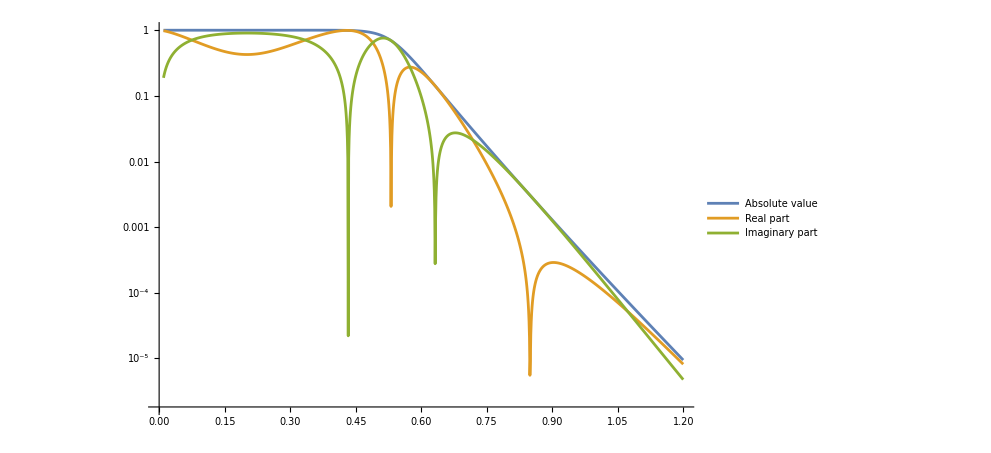

```mathematica
ListLogPlot[{Transpose[{omegaTab,Abs[Rvals]}],Transpose[{omegaTab,Abs[Re[Rvals]]}],Transpose[{omegaTab,Abs[Im[Rvals]]}]},Joined->True,PlotLegends->{"Absolute value","Real part","Imaginary part"}]
```